```mathematica
(*Mathematica*)
```

```mathematica
ph[z_]=-130.66666666666748+1154.2222222222317 z^2-749.7777777777783 z^4+18999.555555555646 z^6+16019.11111111116 z^8+42206.333333333474 z^10+15390.666666666688 z^12+20934.666666666715 z^14-1683.1111111111227 z^16+2571.7777777777806 z^18-454.22222222222297 z^20+105.77777777777779 z^22-18.66666666666666 z^24+z^26
```

-130.667+1154.22 z^2-749.778 z^4+18999.6 z^6+16019.1 z^8+42206.3 z^10+15390.7 z^12+20934.7 z^14-1683.11 z^16+2571.78 z^18-454.222 z^20+105.778 z^22-18.6667 z^24+z^26

```mathematica
w=x/.NSolve[ph[x]==0,x]
```

{-3.14642,-3.14626,-1.36778-1.36778 ⅈ,-1.36778+1.36778 ⅈ,-1.36603-1.36603 ⅈ,-1.36603+1.36603 ⅈ,-0.586368-0.791918 ⅈ,-0.586368+0.791918 ⅈ,-0.57735-0.816497 ⅈ,-0.57735+0.816497 ⅈ,-0.366025-0.366025 ⅈ,-0.366025+0.366025 ⅈ,-0.317837,0.317837,0.366025-0.366025 ⅈ,0.366025+0.366025 ⅈ,0.57735-0.816497 ⅈ,0.57735+0.816497 ⅈ,0.586368-0.791918 ⅈ,0.586368+0.791918 ⅈ,1.36603-1.36603 ⅈ,1.36603+1.36603 ⅈ,1.36778-1.36778 ⅈ,1.36778+1.36778 ⅈ,3.14626,3.14642}

```mathematica
max=Max[Norm/@w]+1
```

4.14642

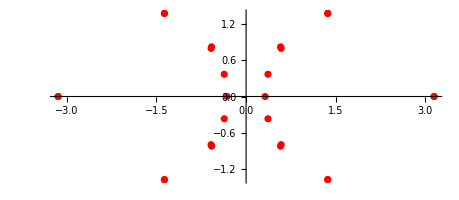

```mathematica
ComplexListPlot[w,PlotStyle->Red,ImageSize->Full]
```

```mathematica
ga=ComplexPlot[ph[z],{z,-max-max*I,max+max*I},ColorFunction->"CyclicReImLogAbs",ImageSize->4000];
```

```mathematica
Export["j_1000_Cube_Rotated45deghrees_Polynomial_z26_scale396p875_ComplexListPlot_ga.jpg",ga]
```

j_1000_Cube_Rotated45deghrees_Polynomial_z26_scale396p875_ComplexListPlot_ga.jpg

```mathematica
Clear[g1,g2]
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by R. L. BAGULA 28 Oct 2026© *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nzold=0},
	For[
		escapeCount = 0,
		(Sqrt[Re[nz]^2+Im[nz]^2] < 32) && (escapeCount < 512) && (Abs[nz-nzold]>.5*10^(-3)),
		nzold=nz;
		nz=ph[nz]/396.875;
        ++escapeCount
	];
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]],Abs[Arg[nz]-Arg[nz]^3/3]]
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-0.6+0.0001,0.6,1000},{-0.6+0.001,0.6,1000}}];
```

```mathematica
g1=ListPlot3D[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction→"Rainbow",Background→Black,ViewPoint→Above,ImageSize->2*{2000,2000}];
```

```mathematica
Export["j_1000_Cube_Rotated45deghrees_Polynomial2_z26_scale396p875_In_Out_monitor_g1.jpg",g1]
```

j_1000_Cube_Rotated45deghrees_Polynomial2_z26_scale396p875_In_Out_monitor_g1.jpg

```mathematica
arraym=FractalPureM[{{-0.6+0.0001,0.6,2000},{-0.6+0.001,0.6,2000}}];
```

```mathematica
Export["j_2000_Cube_Rotated45deghrees_Polynomial2_z26_scale396p875_In_Out_monitor_g2.jpg",g2=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]],
                          Mesh -> False,
		                  AspectRatio -> Automatic,
		                ColorFunction->"Rainbow",ImageSize->2*{2000,2000},Frame->False]]
```

j_2000_Cube_Rotated45deghrees_Polynomial2_z26_scale396p875_In_Out_monitor_g2.jpg

```mathematica
colortab=Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3]];
```

```mathematica
Length[%]
```

542

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/542,1,Ceiling[542*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
Export["j_2000_Cube_Rotated45deghrees_Polynomial2_z26_scale396p875_In_Out_monitor_g3.jpg",g3=ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2*{2000,2000},Frame->False]]
```

j_2000_Cube_Rotated45deghrees_Polynomial2_z26_scale396p875_In_Out_monitor_g3.jpg

```mathematica
Export["j_2000_Cube_Rotated45deghrees_Polynomial3_z26_scale396p875_In_Out_monitor_grid.jpg",GraphicsGrid[{{ga,g2}, 
 {g3,g1}},ImageSize->8000]]
```

j_2000_Cube_Rotated45deghrees_Polynomial3_z26_scale396p875_In_Out_monitor_grid.jpg